## Introducing the Lagrangian and applying Euler’s equation to it

```mathematica
<<VariationalMethods`
```

```mathematica
L[t_]:=1/2(m+M)D[r[t],t]^2+1/2 m*r[t]^2*D[θ[t],t]^2+g*r[t]*(m*Cos[θ[t]]-M)
```

Applying Euler’s equations for both r and θ yields:

```mathematica
EulerEquations[L[t],r[t],t]//TraditionalForm
Expand@EulerEquations[L[t],θ[t],t]//TraditionalForm
```

g m cos(θ(t))-g M-(m+M) r''(t)+m r(t) (θ'(t))^2==0

-g m r(t) sin(θ(t))-2 m r(t) r'(t) θ'(t)-m (r(t))^2 θ''(t)==0

Simplifying the equations by introducing the mass ratio M/m = μ, where M is for the vertically moving ball and m is for the swinging one, and then eliminate the mass from θ equation :

```mathematica
Solve[{EulerEquations[L[t],r[t],t], μ==M/m},r''[t],{M,m}][[1]][[1]]/.Rule->Equal
Solve[Expand@EulerEquations[L[t],θ[t],t],θ''[t]][[1]][[1]]/.Rule->Equal
```

r''[t]==(-g μ+g Cos[θ[t]]+r[t] θ'[t]^2)/(1+μ)

θ''[t]==(-g Sin[θ[t]]-2 r'[t] θ'[t])/r[t]

Solving the differential equation for multiple set of initial conditions with g=9.8 :

```mathematica
g=9.8;
```

```mathematica
Dr[t_]:=NDSolve[{r''[t]==1/(1+μ)(-g μ+g Cos[θ[t]]+r[t] θ'[t]^2),θ''[t]==(-g Sin[θ[t]]-2 r'[t] θ'[t])/r[t],r'[0]==b,θ'[0]==d,r[0]==a,θ[0]==c},{r[t],θ[t]},{t,0,100}]
```

# Plotting the the results in Polar coordinates

### The first set of initial conditions is r_0=1.5, (ṙ)_0=0.6, θ_0=(2π)/3, (θ̇)_0=0, each plot is labeled with the used μ

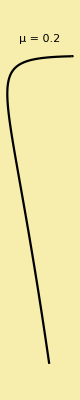
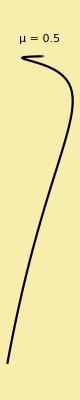
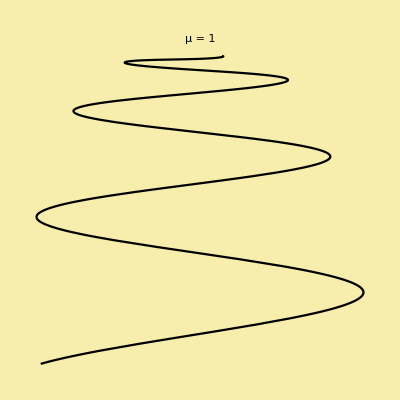
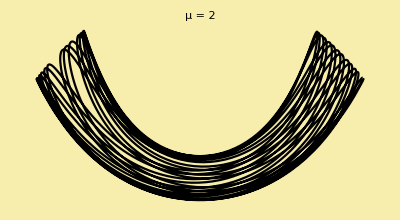
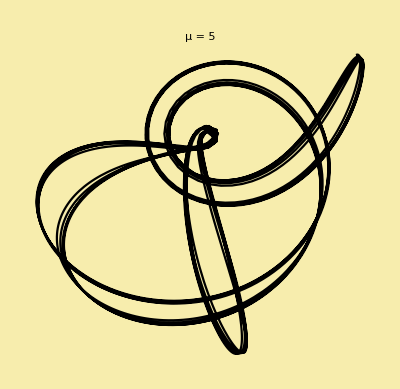

```mathematica
a=1.5;b=0.6;c=(2π)/3; d=0;
μ=0.2;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

g1=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 0.2"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=0.5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

g2=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 0.5"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=1;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

g3=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68],AspectRatio->1],PlotLabel->HoldForm["μ = 1"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=2;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

g4=Show[ParametricPlot[Pr[t][[1]],{t,0,30},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 2"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
μ=5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

g5= Show[ParametricPlot[Pr[t][[1]],{t,0,30},PlotStyle->Black,PlotRange->All,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 5"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
g1 g2 g3 g4 g5
```

### The Second set of initial conditions is r_0=2, (ṙ)_0=0, θ_0=π, (θ̇)_0=1.5, each plot is labeled with the used μ

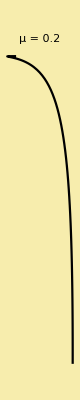
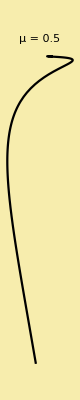
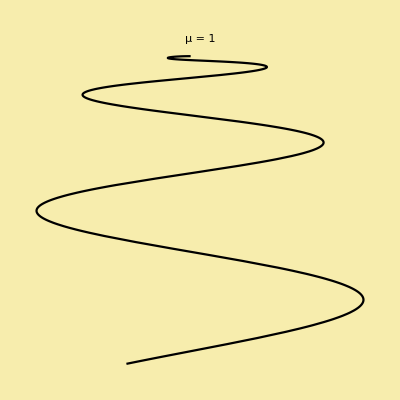
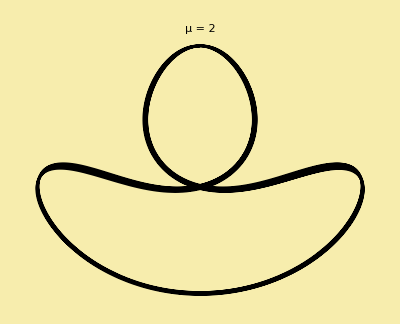
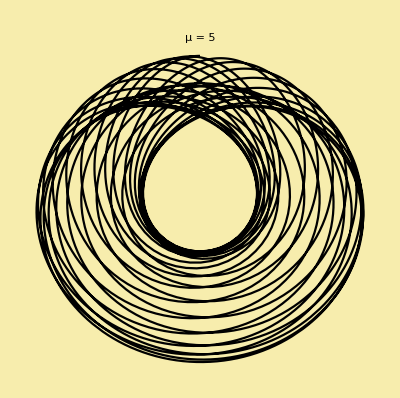

```mathematica
a=2;b=0;c=Pi; d=1.5; 
μ=0.2;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

h1=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 0.2"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=0.5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

h2=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 0.5"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=1;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

h3=Show[ParametricPlot[Pr[t][[1]],{t,0,50},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->1],PlotLabel->HoldForm["μ = 1"],LabelStyle->{Thick},ImageSize->Scaled[0.1],Axes->False,LabelStyle->Opacity[0]];
μ=2;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

h4=Show[ParametricPlot[Pr[t][[1]],{t,0,30},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 2"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
μ=5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]

h5=Show[ParametricPlot[Pr[t][[1]],{t,0,30},PlotStyle->Black,PlotRange->All,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["μ = 5"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
h1 h2 h3 h4 h5
```

### I will now reproduce some of the plots generated in Figure 4 from the paper Professor Bahlouli supplied where the initial conditions are r_0=1, (ṙ)_0=0, θ_0=π/2, (θ̇)_0=0:

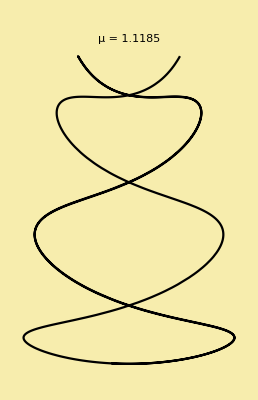
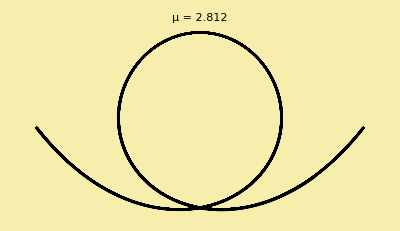
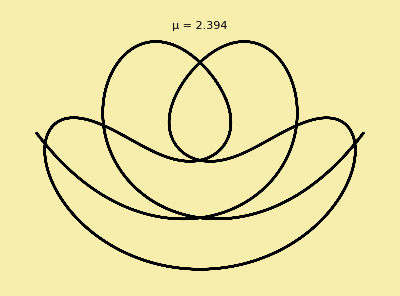

```mathematica
a=1;b=0;c=Pi/2; d=0;
μ=1.1185;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
q1=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 1.1185"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
μ=2.394;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
q2=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 2.394"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
μ=2.812;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
q3=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 2.812"],LabelStyle->{Thick},ImageSize->Scaled[0.2],Axes->False,LabelStyle->Opacity[0]];
q1 q2 q3
```

### For the same set of initial conditions r_0=1, (ṙ)_0=0, θ_0=π/2, (θ̇)_0=0, lets see at which value of μ the trajectory takes a chaotic behavior :

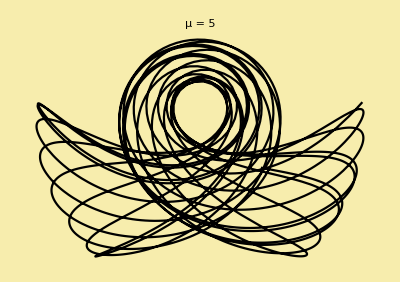
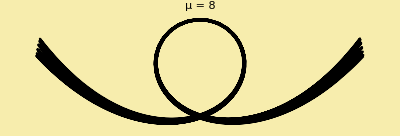
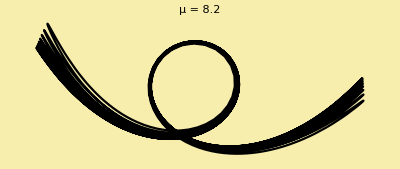
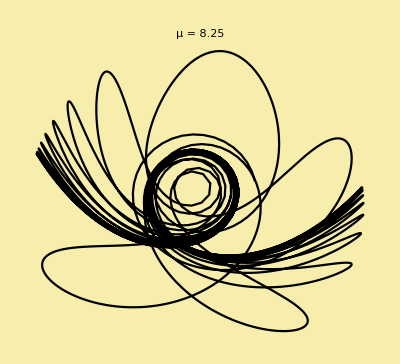
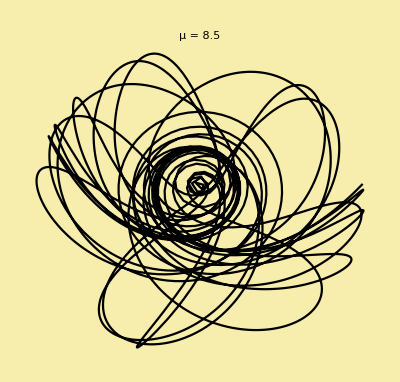
-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-

```mathematica
a=1;b=0;c=Pi/2; d=0;
μ=5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
aa=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 5"],LabelStyle->{Thick},ImageSize->Scaled[0.15],Axes->False,LabelStyle->Opacity[0]];
μ=8;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
bb= Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 8"],LabelStyle->{Thick},ImageSize->Scaled[0.15],Axes->False,LabelStyle->Opacity[0]];
μ=8.2;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
cc=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 8.2"],LabelStyle->{Thick},ImageSize->Scaled[0.15],Axes->False,LabelStyle->Opacity[0]];
μ=8.25;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
dd=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 8.25"],LabelStyle->{Thick},ImageSize->Scaled[0.15],Axes->False,LabelStyle->Opacity[0]];
μ=8.5;
Pr[t_]:=Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.Dr[t]]
ee=Show[ParametricPlot[Pr[t][[1]],{t,0,6Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68], AspectRatio->Automatic],PlotLabel->HoldForm["μ = 8.5"],LabelStyle->{Thick},ImageSize->Scaled[0.15],Axes->False,LabelStyle->Opacity[0]];
aa ->bb->cc->dd->ee
```

## Some Observations: We can observe from the First two sets of plots that when μ is one or less, which means the swinging ball is heavier than the vertical one, the ball will fall indefinity due to gravity. and once it exceeds 1, the trajectory will take a behavior that will not cause the swinging ball to fall indefinity. The third set of plots shows that my work is precise and matches the scientific paper when the same initial conditions is used. The final sets of plots shows that the trajectory of the swinging ball will dramatically be chaotic when μ exceeds 8.5

# Phase diagram & interactive Plot

### Now lets plot the phase diagram for this set of initial conditions r_0=2, (ṙ)_0=1, θ_0=2π, (θ̇)_0=1.5 and this value of μ = 5 :

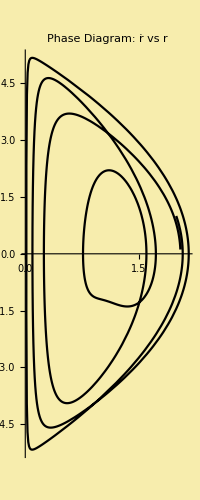

```mathematica
a=2;b=1;c=2Pi; d=1.5; μ=5;
Pr[t_]:=Evaluate[r[t]/.Dr[t]]
ρ[t_]:=(Pr[t+0.0001][[1]]-Pr[t][[1]])/0.0001 (* This is the numerical derivative of r, i.e. ṙ*)
Show[ ParametricPlot[{Pr[t][[1]],ρ[t]},{t,0,2Pi},PlotStyle->Black,Background->RGBColor[0.97,0.93,0.68]],PlotLabel->HoldForm["Phase Diagram: ṙ vs r"],LabelStyle->{Thick},ImageSize->Scaled[0.3],AspectRatio->Full]
```

### Here is the interaction plot, obtained from https://demonstrations.wolfram.com/SwingingAtwoodsMachine/ , with small modifications:

```mathematica
Manipulate[With[{s=NDSolve[{r''[t]==1/(1+μ) (r[t] θ'[t]^2-9.8 (μ-Cos[θ[t]])),θ''[t]==-(2 r'[t] θ'[t])/r[t]-(9.8 Sin[θ[t]])/r[t],r'[0]==rp0,θ'[0]==θp0,r[0]==r0,θ[0]==θ0},{r,θ},{t,0,tf},MaxSteps->∞]},ParametricPlot[Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.s],{t,0,tf},Background->RGBColor[0.97,0.93,0.68],Axes->False,PlotRange->{{-2.5,2.5},{-3.1,2.5}},ImageSize->450,PlotStyle->Red,ImagePadding->{{30,10},{Automatic,Automatic}},Epilog->{Line[{{-1,0},{0,0}}],Line[{{-1.,0},{-1.,-3+r[tf]}/.First[s]}],Disk[{-1,0},.075],Disk[{0,0},.075],PointSize[.035],Rotate[{Line[{{0,0},{r[tf] Cos[θ[tf]],r[tf] Sin[θ[tf]]}/.First[s]}],Green,Point[{r[tf] Cos[θ[tf]]+.1,r[tf] Sin[θ[tf]]}/.First[s]]},-π/2,{0,0}],Cyan,Point[{-1.,-3+r[tf]}/.First[s]]},PlotPoints->100]],
{{tf, 0.1,  Style["t", Italic]}, 0.1, 50, 0.01, AnimationRate->1,
   Appearance -> "Open", ImageSize -> Tiny}, {{μ, 5, "μ"}, 1.26, 12, 0.01, 
   Appearance -> "Labeled", ImageSize -> Tiny}, 
  {{r0, 2, Subscript[Style["r", Italic], 0]}, 0.2, 2, 0.01, Appearance -> "Labeled", 
   ImageSize -> Tiny}, {{θ0, Pi, Subscript["θ", 0]}, 0., 6.28, 0.01, 
   Appearance -> "Labeled", ImageSize -> Tiny}, 
  {{rp0, 0, Row[{Style["r", Italic], "'(0)"}]}, -0.5, 2.62, 0.01, 
   Appearance -> "Labeled", ImageSize -> Tiny}, 
  {{θp0, 1.5, Row[{"θ", "'(0)"}]}, -3., 3., 0.01, 
   Appearance -> "Labeled", ImageSize -> Tiny},ControlPlacement->Left]
```

# Ibraheem Al-Yousef, PHYS300